runDM

With runDMC, it’s Tricky. With runDM, it’s not.

runDM is a tool for calculating the low energy couplings of Dark Matter (DM) to light quarks in Simplified Models with vector mediators. By specifying the mass of the mediator and the couplings of the mediator to SM fields at high energy, the code outputs the low energy couplings to up, down and strange quarks, taking into account the mixing of all dimension-6 operators.

Let’s start by loading in the runDM code.

```mathematica
Get[NotebookDirectory[] <> "runDM.m"];
```

First, let’s specify the couplings at high energy. This will be an 1-D array with 16 elements. runDM comes with a number of pre-defined benchmarks, which can be accessed using setBenchmark.

```mathematica
chigh = setBenchmark["UniversalAxial"];
Print["Axial-vector coupling to all SM fermions: " <> ToString[chigh] ];

chigh = setBenchmark["LeptonsVector"];
Print["Vector coupling to all SM leptons: " <> ToString[chigh]];
```

Axial-vector coupling to all SM fermions: {-1., 1., 1., -1., 1., -1., 1., 1., -1., 1., -1., 1., 1., -1., 1., 0.}

Vector coupling to all SM leptons: {0., 0., 0., 1., 1., 0., 0., 0., 1., 1., 0., 0., 0., 1., 1., 0.}

Alternatively, you can specify each coupling individually. You can use initCouplings[] to generate an empty array of couplings and then go ahead. But any array of 16 elements will do.

```mathematica
chigh = initCouplings[];
chigh[[3]] = 1.0;
chigh[[7]] = -1.0;
Print["User-defined couplings: " <> ToString[chigh]];
```

User-defined couplings: {0, 0, 1., 0, 0, 0, -1., 0, 0, 0, 0, 0, 0, 0, 0, 0}

From these high energy couplings (defined at some energy E_1), you can obtain the couplings at a different energy scale E_2 by using evolveCouplings[c, E_1, E_2]. 

The input coupling vector c should always be the list of high energy couplings to fully gauge-invariant operators above the EW scale (see Eq. ??? of the manual) - even if E_1 is below m_Z. The output is either a list of coefficients for the same operators - if E_2 is above m_Z - or the list of coefficients for the low energy operators (see Eq. ??? of the manual) - if E_2 is below m_Z. Don’t worry, runDM takes care of the relative values of E_1 and E_2.

```mathematica
Subscript[E, 1] = 1000;Subscript[E, 2] = 1;
clow = evolveCouplings[chigh, Subscript[E, 1], Subscript[E, 2]]
```

{0.0110265,0.494488,-0.488974,-0.00551248,-0.00551274,-0.0165405,-0.0165405,-0.0165405,1.53671×10^-6,0.499998,-0.499998,-1.53671×10^-6,-1.27268×10^-6,-1.53671×10^-6,-1.53671×10^-6,-1.53384×10^-6}

If we’re only interested in direct detection experiments, we can use the function lightqCouplings[c, E_1, E_2]. In this case, the output is an array with 6 elements, the vector and axial-vector couplings to light quarks: c_q=(c_V^(u),c_V^(d),c_V^(s),c_A^(u),c_A^(d),c_A^(s)). Let’s calculate them and print them out.

```mathematica
cq = lightqCouplings[chigh, Subscript[E, 1], Subscript[E, 2]];

clabels = {"c_V","c_V", "c_V", "c_A", "c_A", "c_A"};
Grid[Transpose[{clabels, cq}]]
```

c_V | 0.0110265
c_V | 0.494488
c_V | -0.00551248
c_A | 1.53671×10^-6
c_A | 0.499998
c_A | -1.53671×10^-6

Finally, let’s take a look at the value of the low-energy light quark couplings (evaluated at μ_N ~ 1 GeV) as a function of the mediator mass m_V.

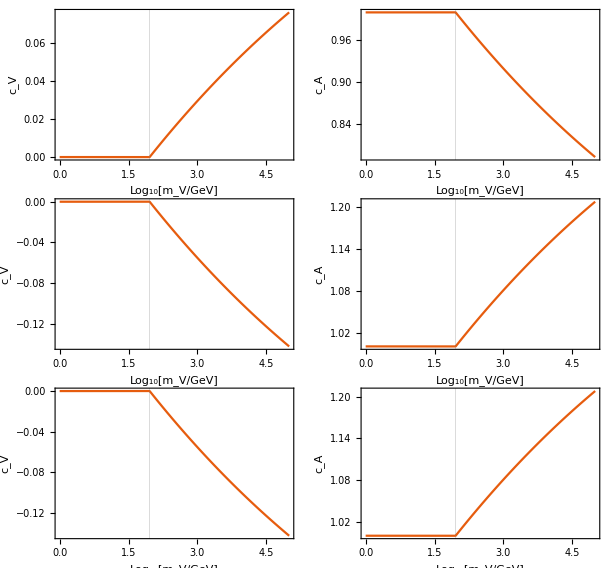

```mathematica
chigh = setBenchmark["QuarksAxial"];

GraphicsGrid[Transpose[ArrayReshape[Table[Plot[{lightqCouplings[chigh,10^Subscript[lm, V], 1.0][[k]]}, {Subscript[lm, V], 0.0, 5.0}, PlotTheme->"Scientific", FrameLabel->{"Log_10[m_V/GeV]", clabels[[k]]}, PlotRangePadding->.1,ImageSize->300, GridLines->{{Log10[91.1875]},{}}, BaseStyle->{FontSize->16}], {k,6}],{2,3}]], Spacings->0.0]
```

1) Direct detection - coupling and mediator mass - automatically run to 1 GeV

2) Coupling, mediator mass, and another scale - full vector

...3...) Input in terms of V and AV below mZ